# Gravitational-Electrostatic Equilibrium

Brian Beckman

June 2026

In this notebook, we conduct a series of thought experiments on gravitation (Newtonian and Einsteinian) and electrostatics (classical and quantum). We begin with the question “what is the radius required for two identical balls separated by 1 meter to exert a static gravitational force of 1 Newton on each other.” We find, by a Newtonian calculation, that they must weigh about 1/√G≈122.4 metric tonnes, and slightly less by General Relativity. 

We evaluate these requirements across six  material densities, spanning terrestrial metals (Osmium, Gold, Lead, Iron) and degenerate astrophysical matter (White Dwarf and Neutron Star cores). 

We then evaluate the feasibility of balancing this gravitational attraction with an equal electrostatic repulsion. For terrestrial metal spheres, achieving this balance is mechanically viable but severely constrained by manufacturing, environmental toxicity, and security logistics, leaving cast steel (Iron) as the only practically executable candidate.

Conversely, for degenerate spheres, the extreme charge concentration required for electrostatic balance creates surface electric fields that far exceed the Fowler-Nordheim threshold, triggering instantaneous quantum field emission (vacuum discharge). Electrostatic pressure remains below the Coulomb explosion threshold for all materials. 

Finally, we model mutual polarization (charge redistribution) using the method of images, demonstrating that while ordinary metal spheres experience a  30% reduction in repulsive force due to polarization—demanding a large reduction in gap distance or an increase in  charge—degenerate spheres remain unaffected due to their sub-millimeter geometries.

## Radius at Density for 1 Newton Grav Force

Ask “given a density ρ of matter, what are the radii required of two identical balls to produce a 1-Newton gravitational force (about 3.6 ounces of force) at a surface-to-surface separation of one meter?”

The center-to-center distance d between the two balls is 1+2R, where R is the radius of a ball. The mass of a ball is its density times its volume:

m=ρ (4π)/3 R^3

One Newton of Newtonian gravitational force is

1=G m^2/d^2=G ((ρ (4π)/3 R^3)/(1+2R))^2

or

3/(4π ρ √G)=R^3/(1+2R)

Code this in Wolfram.

```mathematica
ClearAll[G,R,ρ]
```

```mathematica
With[{G=6.67430*^-11},
forceEqn=(3/(4π ρ √G)==R^3/(1+2R))]
```

29221.9/ρ==R^3/(1+2 R)

Looking at three densities, that of Osmium at 22.6 metric tonnes per cubic meter, of white-dwarf (electron-degenerate) matter at 29.3 million metric tonnes per cubic meter, and at neutron-star (nuclear-degenerate) matter at 400 trillion metric tonnes per cubic meter, we find radii within the normal range of human experience!

Osmium balls will have radii of 1.82 meters (about 6 feet) and weigh 567 metric tonnes each.

Balls of white-dwarf matter would have radii of ≈1 cm and weigh 125 metric tonnes each.

Balls of neutron-star matter would have radii of 41 microns—about half the width of a human hair—and weigh 122.4 metric tonnes.

These quantities are computed below from assumed densities, and are summarized here.

Osmium Mass :  567076.

White-Dwarf Mass :  124867.

Neutron-Star Mass :  122415.

Osmium {ρ,R} :  {22590.,1.8164}

White Dwarf {ρ,R} :  {2.93×10^10,0.0100577}

Neutron Star {ρ,R} :  {4.×10^17,0.000041805}

Both the white-dwarf and neutron-star masses are near the point-mass, R=1, limit value of 1/√G=122.404 metric tonnes:

```mathematica
With[{G=Quantity[6.67430*^-11,"m^3/(kg s^2)"]},
√((Quantity[1,"kg m/s^2"]Quantity[1,"m^2"])/G)]
```

122404. kg

Without doing calculations, we note that any apparatus or electrostatic charges present to maintain separation of the spheres would introduce stress-energy in the space(time) between the spheres, slightly reducing the force produced due to General Relativistic effects. We ignore these effects for now.

### Black Holes?

Our imaginary white-dwarf and neutron-star spheres are not remotely near the Schwarzschild radius for 125 mt, 2Gm/c^2≈2 10^-22 meter. Our imaginary tiny white dwarves and neutron stars are not remotely close to collapsing into black holes.

### From Thought Experiment to Practical Reality

#### Osmium

Of course, it’s not remotely imaginable to have small balls of white-dwarf or neutron-star matter, even though their radii—1 cm and 41 μm—are easy to imagine. It turns out that it’s not practical to have balls of Osmium, Gold, or Lead, either. But it is practical to do this experiment with balls of Iron if you’re willing to put up about $759 M. We explain.

Osmium is rare: the total annual production is about 1 metric tonne per year, mostly as a by-product of Platinum mining, at a market price of about $13 M / tonne The balls would consume the entire world output for 1130 years and cost about $14.5 B.

Osmium metallurgy is difficult: Osmium has a high melting point (3033 °C, or 5491 °F) and is hard and brittle. It cannot be cast in a foundry, nor easily machined. To form large structures of Osmium, such as a 567-tonne sphere, powder-sintering metallurgy and hot isostatic pressing (HIP) are required. A specialized, vacuum-sealed furnace the size of a multi-story building at a cost of a couple of billion dollars, filled with osmium powder at staggering pressures and near-melting temperatures will be required to sinter the powder into a solid mass.

Osmium is toxic: When heated near even trace amounts of oxygen, powdered osmium oxidizes into osmium tetroxide, a volatile, toxic liquid and gas that smells like chlorine. Even at microscopic concentrations in the air, it causes severe lung damage, permanent blindness by staining the cornea, and death. The environmental containment shielding required for a large-scale Osmium refinery alone would cost hundreds of millions of dollars.

The entire Osmium project would cost on the order of $20 B, including transport (see below), about twice the capital expenditure cost of the James Webb Space Telescope or four times cost of the Large Hadron Collider.

We note, in passing, that Osmium has many commercial uses in small amounts. As a trivium, before the era of sapphire and diamond phonograph needles, slippery Osmium alloys were common in phonographs because they were relatively heavy and non-wearing on vinyl grooves of phongraph records.

#### Gold, Lead, Iron

On the other hand, realizing the thought experiment with the required 1600-tonne balls of Iron of the required 10-foot radius would not so upset the geopolitical and environmental equilibria. Projects of this scale are the daily business of shipbuilders. The entire project could be effected for around $750 M. With gold, the project would cost about $91 B, mostly in material value and security, and with lead, about $590 M. Gold and Lead would require significant civil engineering to counteract sagging and fracture of the huge balls, however. Iron would be, by far, the easiest material with which to realize our thought experiments.

Current approximate raw material prices per kg (as of mid-2026)
Osmium: ~$12,860/kg
Gold: ~$75,000/kg (approx $2300-2400/oz—highly variable)
Lead: ~$2.10/kg
Iron (industrial scrap/refined steel scale): ~$0.40/kg

Annual global production in metric tonnes
Osmium: 1
Gold: 3600
Lead: 4500000
Iron: 2500 10^6 (Iron ore/pig iron)

As the density of the material drops, the physical size of the spheres must grow to compensate. This growth pushes the centers of mass further apart, demanding a significantly higher total tonnage to achieve 1-Newton attractive force. However, because Gold, Lead, and Iron are vastly more common than Osmium, we cross the threshold from macro-geopolitical impossibility into mere heavy civil engineering.

The following Tabular summarizes:

```mathematica
Tabular[{
{Style[Row[{"Radius (",Style["R",Italic],") per Sphere"}],Bold],
"1.816 m (5.96 ft)","1.950 m (6.40 ft)","2.488 m (8.16 ft)","2.947 m (9.67 ft)"},{Style[Row[{"Mass (",Style["m",Italic],") per Sphere"}],Bold],"567.1 mt","599.9 mt","731.5 mt","843.7 mt"},
{Style["Material Timetable",Bold],Style["1,134 years",Bold],Style["4 months",Bold],Style["3 hours",Bold],Style["21 seconds",Bold]},
{Style["Raw Material Cost (2 Spheres)",Bold],"$14,585 M","$89,985 M","$3.07 M","$0.68 M"},
{Style["Refining & Forming",Bold],"$1,750 M","$150 M","$25 M","$12 M"},
{Style["Logistics & Transport",Bold],"$150 M","$120 M","$220 M","$260 M"},
{Style["Civil Engineering & Cradle",Bold],"$225 M","$250 M","$350 M","$450 M"},
{Style["Total Project Cost",Bold],Style["≈ $16.71 B",Bold],Style["≈ $90.51 B",Bold],Style["≈ $598.07 M",Bold],Style["≈ $722.68 M",Bold]}},
{"Cost / Project Element","Pure Osmium","Pure Gold","Pure Lead","Pure Iron (Steel Scale)"}]//Dataset
```

#### Detailed Material Assessment

Pure Gold

While gold removes the 1,100-year mining impossibility of osmium (taking only a third of a year’s global output), its raw asset valuation pushes the project budget to a staggering $90.5 Billion.

Refining: Far easier than osmium. Gold melts at a manageable 1064°C and is malleable. It can be cleanly cast into segments and fused together without toxic gas hazards.

Security Logistics: The true hidden nightmare here is the security. Moving 1,200 tonnes of pure gold requires military-grade armored convoys, specialized naval escorts, and an underground bunker with security that rival Fort Knox.

Pure Lead

Lead is dirt cheap ($3.07M for the raw material), but it introduces severe mechanical and structural engineering hurdles.

Structural Failure: Lead is soft and prone to “creep” (gradual deformation under mechanical stress). A 731-tonne sphere of solid lead resting in a cradle will slowly sag under its own weight, flattening out over a few years and ruining perfect spherical geometry.

Cradle: The civil engineering and cradle requirements are uniquely complex for Lead because we would need an active, pressurized fluid or hydraulic cushion support to distribute the weight across the entire bottom half of a sphere to keep it round.

Pure Iron

Iron is the champion of practicality for this thought experiment. It requires the largest physical size (20-foot diameter per ball) and the highest mass (1687 mt), but with Iron, we can take advantage of standard global industrial infrastructure.

Manufacturing: The global steel industry handles this scale daily. The spheres can be cast as solid pieces or thick, concentric shells at any major naval shipyard or heavy industrial foundry (similar to manufacturing a submarine hull or a heavy generator rotor).

Logistics & Engineering: Because Iron can be alloyed for structural integrity (e.g., cast steel), it will hold its shape forever without deformation. Supporting it requires a standard industrial heavy-load foundation. The civil engineering costs are higher simply because of the physical volume and footprint of the nearly 20-foot-wide spheres, but it is a project that any tier-one marine construction company could execute within a couple of years for under $1 Billion total.

#### Transport

Transporting the balls would require a multi-axle, heavy-transport vehicle, like the Scheuerle SPMT (Self-Propelled Modular Transporter), and lifting them would require a max-sized crawler crane like the Liebherr LR 13000.

The following Wolfram code backs up the assertions above.

Osmium Mass :  567076.

Gold Mass :  599903.

Lead Mass :  731460.

Iron Mass :  843735.

White-Dwarf Mass :  124867.

Neutron-Star Mass :  122415.

Osmium {ρ,R} :  {22590.,1.8164}

Gold {ρ,R} :  {19300,1.9505}

Lead {ρ,R} :  {11340,2.48788}

Iron {ρ,R} :  {7874,2.94651}

White Dwarf {ρ,R} :  {2.93×10^10,0.0100577}

Neutron Star {ρ,R} :  {4.×10^17,0.000041805}

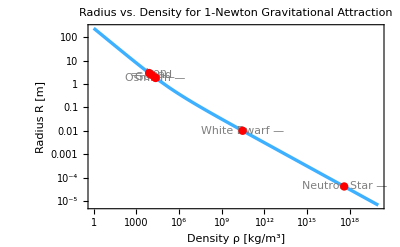

```mathematica
ClearAll[ROfρ,RSoln];
ROfρ[ρIn_]:=(R/.Quiet@Solve[(forceEqn&&ρ>0&&R>0/.{ρ->ρIn}),R,Reals])[[1]];
With[{
osρ=22590.,
goldρ=19300,
leadρ=11340,
ironρ=7874,
wdρ=2.93*^10,
nsρ=4.00*^17},{
osR=ROfρ[osρ],
goldR=ROfρ[goldρ],
leadR=ROfρ[leadρ],
ironR=ROfρ[ironρ],
wdR=ROfρ[wdρ],
nsR=ROfρ[nsρ]},{
osM=Echo[osρ 4π osR^3/3,"Osmium Mass :"],
goldM=Echo[goldρ 4π goldR^3/3,"Gold Mass :"],
leadM=Echo[leadρ 4π leadR^3/3,"Lead Mass :"],
ironM=Echo[ironρ 4π ironR^3/3,"Iron Mass :"],
wdM=Echo[wdρ 4π wdR^3/3,"White-Dwarf Mass :"],
nsM=Echo[nsρ 4π nsR^3/3,"Neutron-Star Mass :"]},
{osmiumPt=Echo[{osρ,osR},"Osmium {ρ,R} :"],
goldPt=Echo[{goldρ,goldR},"Gold {ρ,R} :"],
leadPt=Echo[{leadρ,leadR},"Lead {ρ,R} :"],
ironPt=Echo[{ironρ,ironR},"Iron {ρ,R} :"],
whiteDwarfPt=Echo[{wdρ,wdR},"White Dwarf {ρ,R} :"],
neutronStarPt=Echo[{nsρ,nsR},"Neutron Star {ρ,R} :"]},
LogLogPlot[ROfρ[ρ],{ρ,1,10^20},
PlotRange->All,
PlotStyle->{Thickness[0.006],ColorData[96,1]},
GridLines->Full,
Frame->True,
FrameLabel->{"Density ρ [kg/m^3]","Radius R [m]"},
PlotLabel->Style["Radius vs. Density\nfor 1-Newton Gravitational Attraction",Bold,14],
LabelStyle->Directive[FontSize->12,FontFamily->"Helvetica"],
Epilog->{
Text[Style["Osmium —",Gray,11],Log[osmiumPt],{1,0}],
Text[Style["Gold —",Gray,11],Log[goldPt],{1,2}],
Text[Style["— Lead",Gray,11],Log[leadPt],{-1,-2}],
Text[Style["— Iron",Gray,11],Log[ironPt],{-1,-4}],
Text[Style["White Dwarf — ",Gray,11],Log[whiteDwarfPt],{1,0}],
Text[Style["Neutron Star — ",Gray,11],Log[neutronStarPt],{1,0}],
Directive[Red,PointSize[0.015]],
Point[Log/@{osmiumPt,goldPt,leadPt,ironPt,whiteDwarfPt,neutronStarPt}]}]]
```

```mathematica
G=6.67430*^-11;
ke=8.98755*^9;
```

## Balancing Gravitation with Electrostatics

Now imagine accumulating a sufficient number of electrons on the surfaces of the balls to effect an electrostatic repulsive force of one Newton, counteracting the gravitational force. There are two immediate concerns with even the simplest assumptions: discharge via quantum tunneling (Field Emission, spontaneous vacuum discharge via quantum tunneling) and Coulomb Explosion (charge-induced structural rupture).

### Degenerate Discharge

For white-dwarf and neutron-star spheres, the electric field reaches extreme levels (9.56 × 10⁸  V/m and 5.43 × 10.b9.b3  V/m), resulting in instantaneous field emission discharge.

### Coulomb Explosion

While electrostatic tension

P=1/2 ε_0 E^2

is huge for the neutron-star sphere (≈1.3 × 10.b9⁶  Pa), it is still many orders of magnitude below the astronomical bulk modulus of nuclear matter (≈10.b3.b3  Pa). Therefore, none of the spheres in the 1-Newton configuration explode.

### Computations

The following Wolfram code computes charges, electron counts, electrostatic pressure, and risks for Field Emission and Coulomb Explosion via textbook formulae:

```mathematica
(*Constants*)
G=6.67430*^-11;           (*m^3 kg^-1 s^-2*)
ke=8.98755*^9;             (*N m^2 C^-2*)
eps0=1/(4π ke);         (*F/m*)
eElem=1.602176634*^-19; (*Electron charge in C*)

(*Materials: Name,Density (kg/m^3)*)
materials={{"Pure Osmium",22590.},{"Pure Gold",19300.},{"Pure Lead",11340.},{"Pure Iron",7874.},{"White Dwarf",2.93*^10},{"Neutron Star",4.00*^17}};

(*Formatting Helpers*)
formatDensity[rho_]:=If[rho>=10^6,Row[{ScientificForm[rho,3]," kg/","m^3"}],Row[{NumberForm[rho,NumberSeparator->","]," kg/","m^3"}]];

formatRadius[r_]:=Which[r>=1,Row[{NumberForm[r,{4,3}]," m"}],r>=10^-3,Row[{NumberForm[r*10^3,{4,2}]," mm"}],True,Row[{NumberForm[r*10^6,{4,2}]," μm"}]];

formatMass[m_]:=Row[{NumberForm[m/1000,{4,1}]," t"}];

formatCharge[q_]:=Row[{ScientificForm[q,3]," C"}];

formatElectrons[n_]:=ScientificForm[n,3];

formatField[e_]:=Row[{ScientificForm[e,3]," V/m"}];

formatPressure[p_]:=Which[p>=10^9,Row[{ScientificForm[p,3]," Pa"}],p>=10^6,Row[{NumberForm[p/10^6,{3,2}]," MPa"}],p>=1,Row[{NumberForm[p,{3,2}]," Pa"}],True,Row[{NumberForm[p,{3,3}]," Pa"}]];

(*Compute Data for Each Material Column*)
colsData=
Table[
With[{rho=mat[[2]]},
Module[{R,rVal,mass,charge,electrons,field,pressure,status},
(*Solve Sqrt[G]*M=2R+1 for the unique positive root*)
rVal=R/. First[NSolve[Sqrt[G]*rho*(4/3)*Pi*R^3==2*R+1&&R>0,R]];
(*Calculate secondary quantities*)
mass=((4π)/3 rVal^3)rho;
charge=mass √(G/ke);
electrons=charge/eElem;
field=ke*charge/rVal^2;
pressure=(1/2)*eps0*field^2;
status=If[field<=10^7,Style["Stable",Darker[Green],Bold],Style["Quantum Discharge",Red,Bold]];
(*Output formatted values*)
{formatDensity[rho],formatRadius[rVal],formatMass[mass],formatCharge[charge],formatElectrons[electrons],formatField[field],formatPressure[pressure],status,Style["None",Darker[Green],Bold]}]],{mat,materials}];

(*Table Headers and Row Labels*)
headers=Prepend[materials[[All,1]],"Cost / Project Element"];
rowLabels={"Density (ρ)","Sphere Radius (R)","Sphere Mass (M)","Required Charge (q)","Excess Electrons","Surface E-Field (E)","Electrostatic Pressure (P)","Field Emission Status","Coulomb Explosion Risk"};

(*Rearrange column-major data into row-major grid lines*)
tabularData=
Table[
Prepend[
Table[colsData[[c,r]],{c,1,Length[materials]}],
Style[rowLabels[[r]],Bold]],{r,1,Length[rowLabels]}];

(*Generate Tabular Object*)
Tabular[tabularData,headers]//Dataset
```

### Engineering Challenges for the Electrostatic Experiment

Electrifying massive spheres to achieve gravitational-electrostatic balance introduces several severe practical and engineering challenges.

#### Insulator Load (Material Science)

Each sphere weighs between 560 and 840 metric tonnes. To prevent the electric charge from instantly draining into the Earth, the spheres must sit on electrically insulating cradles.

Materials that are excellent electrical insulators (like Teflon, glass, or alumina ceramics) typically have low fracture toughness or creep under high mechanical loads. Designing a support cradle that can withstand hundreds of tonnes of shear and compressive stress without cracking while maintaining an insulation resistance high enough to block hundreds of kilovolts, is a major materials challenge.

Charge Redistribution (Mutual Polarization)

In basic calculations, we assume the spheres act as point charges. The gravitational and electrostatic forces would balance for any separation (!) because both forces follow inverse-square laws.

However, because they are made of highly conductive metals (especially Gold and Iron), electrons repel each other and migrate to the far sides of the spheres. The resulting polarization shifts the effective “center of charge” outward, away from the physical center of mass.

To maintain balance, the exact separation distance will be much, much smaller than the original 1 meter. The following code estimates the new required separations using the textbook method of images. The resulting table takes a few seconds to compute.

```mathematica
(*Method of Images Force Calculator*)
CalculateForce[R_,d_,Q0_]:=
Module[{maxTerms=30,b,q,S,force,i,j},b=Table[0.,{maxTerms}];
q=Table[0.,{maxTerms}];
b[[1]]=0.;
q[[1]]=1.;
Do[b[[k]]=R^2/(d-b[[k-1]]);
q[[k]]=-q[[k-1]]*R/(d-b[[k-1]]);,
{k,2,maxTerms}];
S=Total[q];
force=0.;
Do[
Do[
force+=(q[[i]]*q[[j]])/(d-b[[i]]-b[[j]])^2;,
{j,1,maxTerms}];,
{i,1,maxTerms}];
ke*Q0^2*force/S^2];
```

```mathematica
(*Compute Polarization Corrections*)
colsData=Table[With[{rho=mat[[2]]},Module[{R,rVal,mass,charge,d0,f0,pctRed,dNew,gNew,deltaG,qRatio},
rVal=R/. First[NSolve[√G rho((4π R^3)/3)==2*R+1&&R>0,R]];
mass=rho*((4π rVal^3)/3);
charge=mass √(G/ke);
d0=2rVal+1;
(*Repulsive force at the original 1-meter gap*)
f0=CalculateForce[rVal,d0,charge];
pctRed=(1.0-f0)*100;
(*Find the closer separation dNew where Force=1 N*)
dNew=d/. First[FindRoot[CalculateForce[rVal,d,charge]==1,{d,d0-0.05}]];
gNew=dNew-2rVal;
deltaG=1.0-gNew;
(*Charge multiplier needed to balance at the original d0*)
qRatio=1.0/√f0;
{Row[{NumberForm[pctRed,{3,2}],"%"}],Row[{NumberForm[gNew,{4,3}]," m"}],Row[{NumberForm[deltaG,{4,3}]," m"}],Row[{NumberForm[(qRatio-1)*100,{3,2}],"%"}]}]],{mat,materials}];

(*Construct Tabular*)
headers=Prepend[materials[[All,1]],"Mutual Polarization Effect"];
rowLabels={"Force Reduction at 1m Gap","New Gap for 1-Newton Repulsion","Gap Decrease Needed","Charge Increase for Balance at 1m"};

tabularData=Table[Prepend[Table[colsData[[c,r]],{c,1,Length[materials]}],Style[rowLabels[[r]],Bold]],{r,1,Length[rowLabels]}];

Tabular[tabularData,headers]//Dataset
```

#### Surface Quality & Corona Discharges

The surface electric fields for these spheres are around 7.5 × 10⁴ to 1.33 × 10⁵  V/m. While this is below the dielectric breakdown of dry air (≈3 × 10⁶  V/m), it is highly vulnerable to local breakdown. Any microscopic scratch, dust particle, or insect landing on the sphere will act as a lightning rod, concentrating the local electric field. Also, field concentration will ionize the surrounding air, leading to a steady, glowing corona discharge that bleeds the charge into the atmosphere. The entire experiment would need to be housed in an ultra-high vacuum (UHV) chamber to maintain charge stability.

#### Background Ionization (Cosmic Rays)

Even in a perfect vacuum, the spheres will slowly lose charge over time. Cosmic rays, solar radiation, and trace radioactive decay in the surrounding containment walls will continuously ionize residual gas in the vacuum chamber. Additionally, ambient light will trigger the photo-electric effect on the metal surfaces, ejecting electrons. We would need an active feedback loop using a high-precision electron gun or Van de Graaff generator to constantly top off the charge.

## Conclusions

Our thought-experiment of the gravitational-electrostatic equilibrium of two massive spheres reveals several fundamental physical and engineering limits:

The Mass Limit of 1-Newton Gravity: As material density scales from steel to nuclear-degenerate matter, the sphere radius required to produce a 1-Newton gravitational force decreases from 2.95  m to 41.8 μ m. The required mass converges from above to the point-mass limit of 1/√G≈122.4  metric tonnes. All configurations remain many orders of magnitude larger than their Schwarzschild radii, avoiding black hole collapse.

Terrestrial Engineering Feasibility: While Osmium is mathematically the most compact stable terrestrial metal, its extreme rarity, high-pressure sintering requirements, and the lethal toxicity of osmium tetroxide make it commercially impossible. Gold is ruled out by astronomical asset costs and military-grade security requirements, while lead fails due to gravitational creep. Cast iron (steel scale) is the only realistic material, requiring a 20-foot diameter, a 1,687-tonne load, and a project cost of ≈$750  M using existing heavy-industrial foundries and shipyard logistics.

Electrostatic Stability and Quantum Limits: To balance gravitational attraction, the spheres must carry a charge-to-mass ratio of√(G/k_e)≈ 8.62 × 10^-11 C/kg. For metallic spheres, the resulting surface electric fields (≈10⁵  V/m) are stable in a vacuum. However, for degenerate matter, the microscopic radii compress the charge, generating fields (10⁹ - 10.b9.b3  V/m) that trigger immediate Fowler-Nordheim quantum tunneling (field emission). Structural disintegration via Coulomb explosion is avoided, as the electrostatic pressure remains below the materials’ bulk moduli.

Mutual Polarization Divergence: When conducting spheres are placed near each other, like charges redistribute to the far hemispheres. This polarization reduces the repulsive force by up to 28.4% for metallic spheres at a 1-meter gap, requiring either a significant decrease in separation (e.g., decreasing the iron gap from 1  m to 0.005  m) or a ≈30% increase in charge. In contrast, degenerate spheres are so compact relative to the 1-meter separation that polarization effects are negligible, allowing them to behave as idealized point charges.

## References

### Field Electron Emission & The Fowler-Nordheim Equation

Fowler, R. H., & Nordheim, L. (1928). "Electron Emission in Intense Electric Fields." Proceedings of the Royal Society of London. Series A, 119(781), 173-181.

This foundational paper describes how high external electric fields warp the potential barrier at a metal/vacuum interface, enabling electrons to quantum tunnel out via what is now known as Fowler-Nordheim tunneling.

### The Coulomb Explosion Effect

Schneider, R., & Rost, J. M. (1994). “Coulomb explosion of intense-laser-produced plasmas.” Physical
Review A, 49(6), 5090.

Purnell, J., et al. (1994). “Coulomb explosion of large gas clusters induced by intense femtosecond laser pulses.”
Physical Review Letters, 72(13), 2030.

While commonly studied in laser-plasma physics and cluster ionization, where rapid stripping of electrons leaves behind a highly concentrated, mutually repulsive positive charge core, the classical electrostatics of structural mechanical failure due to surface charge pressure P=(1/2)ε_o E^2 follows identical dynamic fragmentation principles.